## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs4=GenAll[4];Length[baseGraphs4]
```

127

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 4 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations4=CompleteRelations[baseGraphs4];Length[withRelations4]
```

127

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 14 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations4[k,"graph"],k],{k,Take[Keys[withRelations4],20]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-36}

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs4=Select[Reverse[Keys[withRelations4]],CompleteGraphQ[withRelations4[#,"graph"]]&];Length[completeGraphs4]
```

15

```mathematica
42
```

42

```mathematica
baseGraphAxioma4=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->PartitionToSymbol[withRelations4[k,"vertexsets"]],{k,completeGraphs4}]]
```

{x728→v1234,x697→v123x4,x637→v124x3,x608→v12x34,x607→v12x3x4,x473→v134x2,x448→v13x24,x445→v13x2x4,x400→v14x23,x391→v14x2x3,x377→v1x234,x373→v1x23x4,x367→v1x24x3,x365→v1x2x34,x364→v1x2x3x4}

Now we get some lists of variables

```mathematica
allGraphVariables4=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations4]}];Length[allGraphVariables4]
```

127

```mathematica
baseGraphAxioma4Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma4]]]];Length[baseGraphAxioma4Vars]
```

15

```mathematica
baseKeys4=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma4]
```

{728,697,637,608,607,473,448,445,400,391,377,373,367,365,364}

```mathematica
Table[Labeled[withRelations4[k,"graph"],k],{k,baseKeys4}]
```

{-Graphics-728,-Graphics-697,-Graphics-637,-Graphics-608,-Graphics-607,-Graphics-473,-Graphics-448,-Graphics-445,-Graphics-400,-Graphics-391,-Graphics-377,-Graphics-373,-Graphics-367,-Graphics-365,-Graphics-364}

```mathematica
Take[baseGraphAxioma4Vars,4]
```

{v1234,v123x4,v124x3,v12x34}

We now take all relations.  Then we combined this with the base graph axioms.  This gives a huge expression list of 7407 equations

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations4[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma4],
{key,baseKeys4}
],key];
```

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 42 base variables.
This procedure only works fior the b01... variables since we need 4 vertices for the current implementation

```mathematica
withColorTables4=withRelations4;
```

```mathematica
Length[Keys[withRelations4]]
```

127

```mathematica
1894
```

1894

```mathematica
GenerateColorTable4[assocs_,key_]:=Block[
{mat=assocs[key]["matrix"], comb, colofour=assocs[key]["colofour"],newsym,value},

comb=Subsets[Range[4],{2}];
Table[
value=mat[[c[[1]],c[[2]]]];
If[value==2,
{colofour,0},
If[value==1,
{0,colofour},
newsym=Symbol["x"<>ToString[key]<>"y"<>ToString[c[[1]]]<>"z"<>ToString[c[[2]]]];
{newsym,colofour-newsym}
]
]
,{c,comb}
]
]
```

Example of one color table:

```mathematica
GenerateColorTable4[withColorTables4,2]
```

{{x2y1z2,-x2y1z2+Missing[KeyAbsent,colofour]},{x2y1z3,-x2y1z3+Missing[KeyAbsent,colofour]},{x2y1z4,-x2y1z4+Missing[KeyAbsent,colofour]},{x2y2z3,-x2y2z3+Missing[KeyAbsent,colofour]},{x2y2z4,-x2y2z4+Missing[KeyAbsent,colofour]},{Missing[KeyAbsent,colofour],0}}

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys4=baseKeys4;
```

```mathematica
baseGraphAxioma4Vars
```

{v1234,v123x4,v124x3,v12x34,v12x3x4,v134x2,v13x24,v13x2x4,v14x23,v14x2x3,v1x234,v1x23x4,v1x24x3,v1x2x34,v1x2x3x4}

```mathematica
Monitor[Table[
withColorTables4[k]["colortable"]=GenerateColorTable4[withColorTables4,k]
,
{k,baseGraphKeys4}
],k];
```

```mathematica
Keys[withColorTables4[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links}

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable4[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables4[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables4[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables4[r1],"colortable"],
withColorTables4[r1,"colortable"]=TryComputeColourTable4[r1],
];
If[!KeyExistsQ[withColorTables4[r2],"colortable"],
withColorTables4[r2,"colortable"]=TryComputeColourTable4[r2],

];
withColorTables4[k,"colortable"]=withColorTables4[r1,"colortable"]+withColorTables4[r2,"colortable"];
withColorTables4[k,"colofour"]=withColorTables4[r1,"colofour"]+withColorTables4[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables4[k]["relations"]}
]
];
withColorTables4[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables4[0],"colortable"]
```

False

```mathematica
TryComputeColourTable4[0]
```

{{v1234+v123x4+v124x3+v12x34+v12x3x4,v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v123x4+v134x2+v13x24+v13x2x4,v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v124x3+v134x2+v14x23+v14x2x3,v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v123x4+v14x23+v1x234+v1x23x4,v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v124x3+v13x24+v1x234+v1x24x3,v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4},{v1234+v12x34+v134x2+v1x234+v1x2x34,v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4}}

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables4[k]["colortable2"]=withColorTables4[k]["colortable"]
,
{k,Keys[withColorTables4]}
],k];
```

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp4=withColorTables4;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp4[k,"comp"]=GreaterEqual;withRelations4[k,"comp"]="No IH";k,{k,Keys[withComp4]}]//Length
```

127

```mathematica
1894
```

1894

If a base graph is not planar by itself then the  "comp" should be Equal

```mathematica
Table[withComp4[k,"comp"]=Equal;withRelations4[k,"comp"]="Contains K4";k,{k,Select[baseKeys4,!PlanarGraphQ[withComp4[#,"graph"]]&]}]//Length
```

0

```mathematica
IsPlanarSet[set_,total_]:=Block[{result,sot=set-1,breaks=0,i,previous},
If[Length[set]==1,
result=True,
For[i=2,i≤Length[sot],i++,
If[Mod[sot[[i-1]]+1,total]≠Mod[sot[[i]],total],
breaks++;
]
];
If[Mod[sot[[Length[sot]]]+1,total]≠Mod[sot[[1]],total],
breaks++;
];
result=breaks<2;
];
result
]
```

```mathematica
IsPlanarContraction[assoc_,key_]:=Block[{total},
total=Length[Flatten[assoc[key,"vertexsets"]]];
Fold[And,Table[IsPlanarSet[s,total],{s,assoc[key,"vertexsets"]}]]
];
```

```mathematica
Table[If[
IsPlanarContraction[withComp4,k],
withComp4[k,"comp"]=Greater;
withComp4[k,"compWHY"]="Planar contraction";
1,
0]
,{k,baseKeys4}]
```

{1,1,1,1,1,1,0,0,1,1,1,1,0,1,1}

## I am certainly not sure about K4

```mathematica
withComp4[364,"comp"]=GreaterEqual;withComp4[364,"compwhy"]="not sure about planar contraction";withComp4[364]
```

<|signature→364,matrix→{{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4}},vertices→{1,2,3,4},edges→{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}},relations→{x364==x121-x607,x364==x283-x445,x364==x337-x391,x364==x355-x373,x364==x361-x367,x364==x363-x365},links→{},colofour→v1x2x3x4,colortable→{{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4}},colortable2→{{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4}},comp→GreaterEqual,compWHY→Planar contraction,compwhy→not sure about planar contraction|>

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right], result=current},
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
Print["Changing ", key, " to ",result],
]
];
result
]
```

```mathematica
RecalculateComp4[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current},
current=withComp4[k];
If[depth<maxdepth && ! current["marked"],
withComp4[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
RecalculateComp4[r1,depth+1,maxdepth];
withComp4[r1,"parents"]=Append[withComp4[r1,"parents"],k];
RecalculateComp4[r2,depth+1,maxdepth];
withComp4[r2,"parents"]=Append[withComp4[r2,"parents"],k];
withComp4[k,"children"]=Append[withComp4[k,"children"],{r1,r2}];
withComp4[k,"comp"]= MayBeReassign[k,withComp4[k,"comp"], withComp4[r1,"comp"],withComp4[r2,"comp"]]
];
]
,{r,withComp4[k]["relations"]}
];
];withComp4[k,"comp"]
]
```

```mathematica
Table[withComp4[k,"marked"]=False;withComp4[k,"parents"]={};withComp4[k,"children"]={};k,{k,Keys[withComp4]}];markCount=0
```

0

```mathematica
Table[withComp4[k,"comp"]=Equal;withRelations4[k,"comp"]="Contains K4";k,{k,Select[baseKeys4,!PlanarGraphQ[withComp4[#,"graph"]]&]}]//Length
```

0

```mathematica
Monitor[RecalculateComp4[0,0,20],markCount]
```

Changing 363 to Greater

Changing 360 to Greater

Changing 369 to Greater

Changing 351 to Greater

Changing 354 to Greater

Changing 355 to Greater

Changing 357 to Greater

Changing 352 to Greater

Changing 353 to Greater

Changing 382 to Greater

Changing 324 to Greater

Changing 333 to Greater

Changing 336 to Greater

Changing 337 to Greater

Changing 334 to Greater

Changing 342 to Greater

Changing 346 to Greater

Changing 327 to Greater

Changing 328 to Greater

Changing 325 to Greater

Changing 417 to Greater

Changing 414 to Greater

Changing 243 to Greater

Changing 270 to Greater

Changing 279 to Greater

Changing 282 to Greater

Changing 273 to Greater

Changing 274 to Greater

Changing 276 to Greater

Changing 271 to Greater

Changing 309 to Greater

Changing 300 to Greater

Changing 252 to Greater

Changing 255 to Greater

Changing 256 to Greater

Changing 257 to Greater

Changing 253 to Greater

Changing 246 to Greater

Changing 247 to Greater

Changing 244 to Greater

Changing 245 to Greater

Changing 577 to Greater

Changing 487 to Greater

Changing 517 to Greater

Changing 488 to Greater

Changing 486 to Greater

Changing 576 to Greater

Changing 606 to Greater

Changing 666 to Greater

Changing 516 to Greater

Changing 546 to Greater

Changing 0 to Greater

Changing 165 to Greater

Changing 193 to Greater

Changing 168 to Greater

Changing 162 to Greater

Changing 190 to Greater

Changing 218 to Greater

Changing 81 to Greater

Changing 108 to Greater

Changing 117 to Greater

Changing 120 to Greater

Changing 121 to Greater

Changing 122 to Greater

Changing 118 to Greater

Changing 111 to Greater

Changing 112 to Greater

Changing 109 to Greater

Changing 110 to Greater

Changing 145 to Greater

Changing 136 to Greater

Changing 90 to Greater

Changing 93 to Greater

Changing 94 to Greater

Changing 97 to Greater

Changing 91 to Greater

Changing 84 to Greater

Changing 85 to Greater

Changing 87 to Greater

Changing 82 to Greater

Changing 27 to Greater

Changing 36 to Greater

Changing 39 to Greater

Changing 40 to Greater

Changing 37 to Greater

Changing 45 to Greater

Changing 49 to Greater

Changing 30 to Greater

Changing 31 to Greater

Changing 28 to Greater

Changing 63 to Greater

Changing 72 to Greater

Changing 54 to Greater

Changing 18 to Greater

Changing 22 to Greater

Changing 26 to Greater

Changing 9 to Greater

Changing 12 to Greater

Changing 13 to Greater

Changing 14 to Greater

Changing 16 to Greater

Changing 10 to Greater

Changing 3 to Greater

Changing 4 to Greater

Changing 6 to Greater

Changing 1 to Greater

Changing 2 to Greater

Greater

```mathematica
Keys[withComp4[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,marked,parents,children}

```mathematica
withComp4[1,"children"]
```

{{244,487},{190,82},{136,28},{10,22},{16,4}}

```mathematica
{{19684,39367},{13123,6462},{2188,4104},{3646,730},{244,487},{190,82},{136,28},{10,22},{16,4}}
```

{{19684,39367},{13123,6462},{2188,4104},{3646,730},{244,487},{190,82},{136,28},{10,22},{16,4}}

```mathematica
Select[Keys[withComp4],withComp4[#,"comp"]==GreaterEqual&]//Length
```

9

```mathematica
CosyPrint4[key_]:=With[
{current=withComp4[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{100,100}]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]]]
]
```

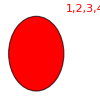
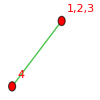
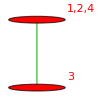
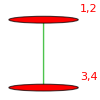
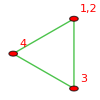
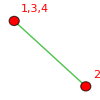
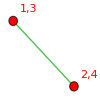
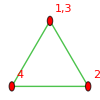
{-Graphics-{728→v1234,1/6},-Graphics-{697→v123x4,1/2},-Graphics-{637→v124x3,1/2},-Graphics-{608→v12x34,1/2},-Graphics-{607→v12x3x4,1},-Graphics-{473→v134x2,1/2},-Graphics-{448→v13x24,1/2},-Graphics-{445→v13x2x4,1},-Graphics-{400→v14x23,1/2},-Graphics-{391→v14x2x3,1},-Graphics-{377→v1x234,1/2},-Graphics-{373→v1x23x4,1},-Graphics-{367→v1x24x3,1},-Graphics-{365→v1x2x34,1},-Graphics-{364→v1x2x3x4,1}}

```mathematica
Table[CosyPrint4[k],{k,baseKeys4}]
```

## We now replace some of the "b" variables with our greek letters

```mathematica
stubbornForm4=withComp4;
```

```mathematica
Keys[stubbornForm4[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,marked,parents,children}

```mathematica
CosyPrintThree4[key_]:=ColorTablePrint[key,stubbornForm4,"colofour","colortable2"]
```

```mathematica
stubbornKeys4=Select[Keys[stubbornForm4],stubbornForm4[#,"comp"]==GreaterEqual&];
```

```mathematica
Length[stubbornKeys4]
```

9

```mathematica
Table[CosyPrint4[k],{k,Intersection[baseKeys4,stubbornKeys4]}]
```

{-Graphics-{364→v1x2x3x4,1},-Graphics-{367→v1x24x3,1},-Graphics-{445→v13x2x4,1},-Graphics-{448→v13x24,1/2}}

```mathematica
stubbornForm4[448,"parents"]
```

{414,442,286,276,168,190,16}

```mathematica
Table[Table[k->p,{p,Select[Flatten[stubbornForm4[k,"parents"]],MemberQ[stubbornKeys4,#]&]}],{k,stubbornKeys4}]
```

{{},{283→280},{286→280},{361→280},{364→361,364→283},{367→361,367→286},{442→280},{445→442,445→283},{448→442,448→286}}

```mathematica
stubbornForm4[280,"colofour"]*2-(stubbornForm4[283,"colofour"]+stubbornForm4[361,"colofour"])//Simplify
```

2 v13x24+v13x2x4+v1x24x3

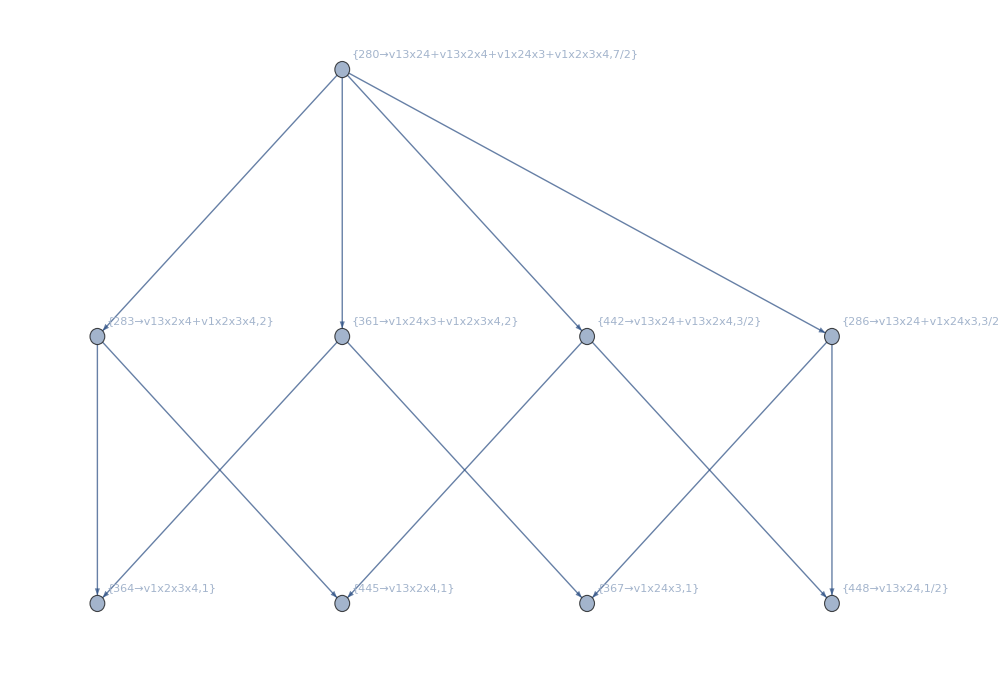

```mathematica
Graph[DeleteDuplicates[Table[
Join[Table[p->k,{p,Select[Flatten[stubbornForm4[k,"parents"]],MemberQ[stubbornKeys4,#]&]}],Table[k->p,{p,Select[Flatten[stubbornForm4[k,"children"]],MemberQ[stubbornKeys4,#]&]}]]
,{k,stubbornKeys4}]//Flatten],VertexLabels->Table[k->CosyPrint4[k],{k,stubbornKeys4}],ImageSize->1000]
```

```mathematica
Table [Labeled[stubbornForm4[k2,"graph"],stubbornForm4[k2,"colofour"]],{k2,stubbornKeys4}]
```

{-Graphics-v13x24+v13x2x4+v1x24x3+v1x2x3x4,-Graphics-v13x2x4+v1x2x3x4,-Graphics-v13x24+v1x24x3,-Graphics-v1x24x3+v1x2x3x4,-Graphics-v1x2x3x4,-Graphics-v1x24x3,-Graphics-v13x24+v13x2x4,-Graphics-v13x2x4,-Graphics-v13x24}

```mathematica
Table [Labeled[stubbornForm4[k2,"graph"],stubbornForm4[k2,"colofour"]],{k2,baseGraphKeys4}]
```

{-Graphics-v1234,-Graphics-v123x4,-Graphics-v124x3,-Graphics-v12x34,-Graphics-v12x3x4,-Graphics-v134x2,-Graphics-v13x24,-Graphics-v13x2x4,-Graphics-v14x23,-Graphics-v14x2x3,-Graphics-v1x234,-Graphics-v1x23x4,-Graphics-v1x24x3,-Graphics-v1x2x34,-Graphics-v1x2x3x4}

```mathematica
ineqsthree4=Table[stubbornForm4[k]["comp"][stubbornForm4[k]["colofour"],0],{k,Keys[stubbornForm4]}]//Simplify;
```

```mathematica
Take[ineqsthree4,4]
```

{v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0,v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0,v1234+v12x34+v134x2+v1x234+v1x2x34>0,v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4>0}

```mathematica
ineqsthree42=Simplify[Fold[And,ineqsthree4]];Length[ineqsthree42]
```

15

```mathematica
graphicsthree=Map[stubbornForm4[#,"colofour"]->stubbornForm4[#,"graph"]&,Select[Keys[stubbornForm4],Length[ListofVars[stubbornForm4[#,"colofour"]]]==1&]];graphicsthree
```

{v1x2x3x4→-Graphics-,v1x2x34→-Graphics-,v1x24x3→-Graphics-,v1x23x4→-Graphics-,v1x234→-Graphics-,v14x2x3→-Graphics-,v14x23→-Graphics-,v13x2x4→-Graphics-,v13x24→-Graphics-,v134x2→-Graphics-,v12x3x4→-Graphics-,v12x34→-Graphics-,v124x3→-Graphics-,v123x4→-Graphics-,v1234→-Graphics-}

```mathematica
graphicsthree2=Map[stubbornForm4[#,"colofour"]->stubbornForm4[#,"graph"]&,Keys[stubbornForm4]];
```

```mathematica
ExpressionToTable2[ineqsthree42]
```

v1x234>0
v1234>0
v14x2x3>0
v13x2x4≥0
v1x2x3x4≥0
v1x23x4>0
v12x3x4>0
v123x4>0
v134x2>0
v1x24x3≥0
v124x3>0
v14x23>0
v13x24≥0
v1x2x34>0
v12x34>0